```mathematica
三个轮子
```

```mathematica
x=x0+a1 Sin[ω0 t+φ1]+a2 Sin[2ω0 t+φ2]+
a3 Sin[3ω0 t+φ3]
y=y0+a1 Cos[ω0 t+φ1]+a2 Cos[2ω0 t+φ2]+
a3 Cos[3ω0 t+φ3]
p=x+y*ⅈ
   =(x0+y0*ⅈ)+a1 (Sin[ω0 t+φ1]+Cos[ω0 t+φ1]*ⅈ)+a2 (Sin[2ω0 t+φ2]+Cos[2ω0 t+φ2]*ⅈ)+
a3 (Sin[3ω0 t+φ3]+Cos[3ω0 t+φ3]*ⅈ)
   =p0+p1+p2+p3
```

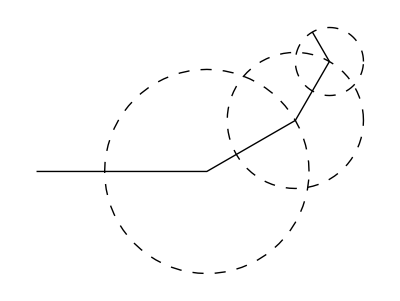

```mathematica
g1=Graphics[{Thick,Line[{{0,0},{5,0},{5,0}+3{Cos[π/6],Sin[π/6]},{5,0}+3{Cos[π/6],Sin[π/6]}+2{Cos[π/3],Sin[π/3]},{5,0}+3{Cos[π/6],Sin[π/6]}+2{Cos[π/3],Sin[π/3]}+{Cos[2π/3],Sin[2π/3]}}]}];
g2=Graphics[{Thick,Dashing[{0.02,0.02}],{Circle[{5,0},3],Circle[{5,0}+3{Cos[π/6],Sin[π/6]},2],Circle[{5,0}+3{Cos[π/6],Sin[π/6]}+2{Cos[π/3],Sin[π/3]},1]}}];
Show[g1,g2]
Clear[g1,g2]
```